## include par in output

```mathematica
PacletDirectoryAdd["~/github/EcoEvo"];
<<EcoEvo`
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

EcoEvo Package Version 1.8.0 (August 16, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Pop[n]->{Equation:>n(1-n/nk)-an p n/(n+h),Color->Green},
Pop[p]->{Equation:>p(apred n/(n+h)-mp),Color->Red},
Parameters:>{an>0,apred>0,h>0,mp>0,nk>0}
}];

RuleListSet@{an->1,apred->2,h->1,mp->1}
```

```mathematica
tr=TrackEcoEq[{n->1,p->2/11,nk->1.1},{nk,1,4},Method->"Direct"]
```

TrackEq::chst: Stability change at nk=1., eigenvalues={-0.999998,0}.

TrackEq::chst: Stability change at nk=3.00017, eigenvalues={0.+0.577383 ⅈ,0.-0.577383 ⅈ}.

{{n→InterpolatingFunction[…][nk],p→InterpolatingFunction[…][nk]},{n→InterpolatingFunction[…][nk],p→InterpolatingFunction[…][nk]}}

```mathematica
tr=TrackEcoEq[{n->1,p->2/11,nk->1.1},{nk,1,4}]
```

TrackEq::chst: Stability change at nk=3.00001, eigenvalues={0.+0.577352 ⅈ,0.-0.577352 ⅈ}.

{{n→InterpolatingFunction[…][nk],p→InterpolatingFunction[…][nk]},{n→InterpolatingFunction[…][nk],p→InterpolatingFunction[…][nk]}}

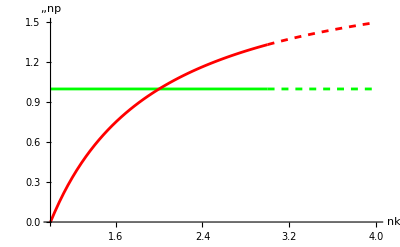

```mathematica
PlotEcoEq[tr]
```

```mathematica
tr=TrackEcoEq[{n->1,p->0.181818},{nk->1.1},{nk,1,4}]
```

TrackEq::chst: Stability change at nk=3.00001, eigenvalues={0.+0.577352 ⅈ,0.-0.577352 ⅈ}.

{{n→InterpolatingFunction[…][nk],p→InterpolatingFunction[…][nk]},{n→InterpolatingFunction[…][nk],p→InterpolatingFunction[…][nk]}}

```mathematica
EcoStableQ[{nk->2},Slice[tr[[1]],2]]
```

True

```mathematica
EcoStableQ[tr[[1]]]
```

True

```mathematica
EcoStableQ[tr]
```

{True,False}

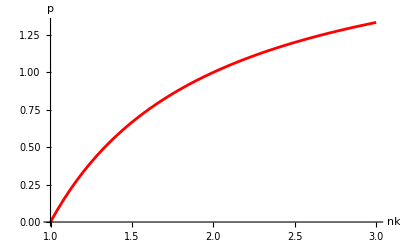

```mathematica
PlotEcoEq[tr[[1]],p,{nk,1,3}]
```

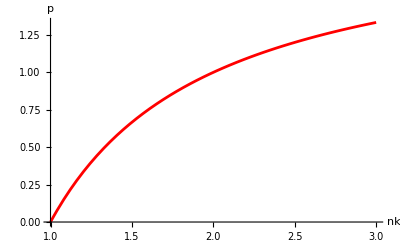

```mathematica
PlotEcoEq[tr[[1]],p]
```

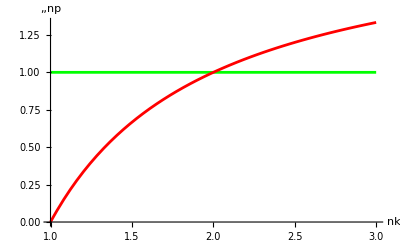

```mathematica
PlotEcoEq[tr[[1]],{n,p}]
```

```mathematica
ParametricRuleListQ[tr[[1]]]
```

True

```mathematica
FinalSlice[tr[[1]]]
```

{n→1.,p→1.33334}

```mathematica
EcoStableQ[tr[[1]]]
EcoStableQ[tr[[2]]]
```

True

False

```mathematica
sol=SolveEcoEq[]
```

{{n→0,p→0},{n→nk,p→0},{n→1,p→(2 (-1+nk))/nk}}

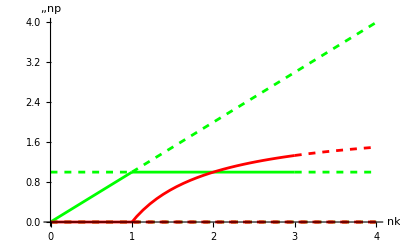

```mathematica
PlotEcoEq[sol,{nk,0,4}]
```

```mathematica
ev=Interpolation[Table[{par,EcoEigenvalues[{nk->par},Slice[tr[[1]],par]]},{par,1,3,0.01}]]
```

InterpolatingFunction[…]

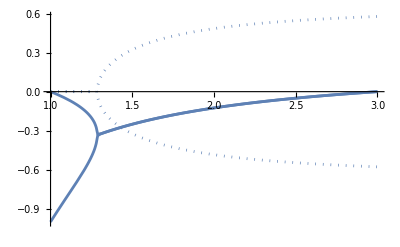

```mathematica
ReImPlot[ev[nk],{nk,1,3}]
```

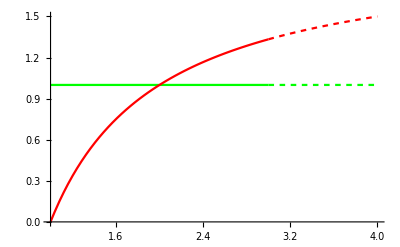

```mathematica
Show[
PlotRuleList[tr[[1]],{n,p}],
PlotRuleList[tr[[2]],{n,p},LineStyles->Dashing[0.01]],
PlotRange->All
]
```

```mathematica
Table[{par,EcoEigenvalues[{nk->par},Slice[tr[[1]],par]]},{par,1,2,0.1}]
```

{{1.,{-1.,-7.13501×10^-6}},{1.1,{-0.807334,-0.056302}},{1.2,{-0.614357,-0.135643}},{1.3,{-0.326924+0.0922343 ⅈ,-0.326924-0.0922343 ⅈ}},{1.4,{-0.285714+0.247436 ⅈ,-0.285714-0.247436 ⅈ}},{1.5,{-0.249996+0.322739 ⅈ,-0.249996-0.322739 ⅈ}},{1.6,{-0.218753+0.373702 ⅈ,-0.218753-0.373702 ⅈ}},{1.7,{-0.191173+0.411495 ⅈ,-0.191173-0.411495 ⅈ}},{1.8,{-0.166667+0.44096 ⅈ,-0.166667-0.44096 ⅈ}},{1.9,{-0.144737+0.464644 ⅈ,-0.144737-0.464644 ⅈ}},{2.,{-0.125+0.484123 ⅈ,-0.125-0.484123 ⅈ}}}

```mathematica
FinalSlice[tr[[1]]]
InitialSlice[tr[[2]]]
```

{n→1.,p→1.33334}

{n→1.,p→1.33334}

```mathematica
Slice[tr[[2]],3.2]
```

{n→1.,p→1.375}

## TrackEq

```mathematica
TrackEq[EcoEqns[],{n->1,p->2/11},{nk,1.1,1,4},Method->"Direct"]
```

rhs={n (1-n/nk)-(n p)/(1+n),(-1+(2 n)/(1+n)) p}

unks={n,p}

rhs={n (1-n/nk)-(n p)/(1+n),(-1+(2 n)/(1+n)) p}

j={{1-(2 n)/nk+(n p)/(1+n)^2-p/(1+n),-n/(1+n)},{(-(2 n)/(1+n)^2+2/(1+n)) p,-1+(2 n)/(1+n)}}

ics={n[1.1]==1.,p[1.1]==0.181818}

deqns={(1-n[nk]/nk) n'[nk]+(n[nk] p[nk] n'[nk])/(1+n[nk])^2-(p[nk] n'[nk])/(1+n[nk])+n[nk] (n[nk]/nk^2-n'[nk]/nk)-(n[nk] p'[nk])/(1+n[nk])==0,p[nk] (-(2 n[nk] n'[nk])/(1+n[nk])^2+(2 n'[nk])/(1+n[nk]))+(-1+(2 n[nk])/(1+n[nk])) p'[nk]==0}

TrackEq::chst: Stability change at nk=1., eigenvalues={-0.999998,0}.

TrackEq::chst: Stability change at nk=3.00017, eigenvalues={0.+0.577383 ⅈ,0.-0.577383 ⅈ}.

{n→InterpolatingFunction[…],p→InterpolatingFunction[…]}

```mathematica
TrackEq[EcoEqns[],{n->1,p->2/11},{nk,1.1,1,4},Method->"PseudoArcLength"]
```

rhs={n (1-n/nk)-(n p)/(1+n),(-1+(2 n)/(1+n)) p}

unks={n,p}

rhs={n (1-n/nk)-(n p)/(1+n),(-1+(2 n)/(1+n)) p}

j={{1-(2 n)/nk+(n p)/(1+n)^2-p/(1+n),-n/(1+n)},{(-(2 n)/(1+n)^2+2/(1+n)) p,-1+(2 n)/(1+n)}}

ics={n[0]==1.,p[0]==0.181818,nk[0]==1.1}

whenevents=

{WhenEvent[nk[EcoEvo`Private`s]==1,StopIntegration],WhenEvent[nk[EcoEvo`Private`s]==4,StopIntegration],WhenEvent[nk'[EcoEvo`Private`s]==0,AppendTo[EcoEvo`Private`breaks$101689,EcoEvo`Private`s]],WhenEvent[EcoEvo`Private`maxev$101689[nk[EcoEvo`Private`s],{n[EcoEvo`Private`s],p[EcoEvo`Private`s]}]==0,Message[TrackEq::chst,EcoEvo`Private`parname$101689,nk[EcoEvo`Private`s],Chop[EcoEvo`Private`evs$101689]];AppendTo[EcoEvo`Private`breaks$101689,EcoEvo`Private`s]]}

deqns=

{n[EcoEvo`Private`s] (1-n[EcoEvo`Private`s]/nk[EcoEvo`Private`s])-(n[EcoEvo`Private`s] p[EcoEvo`Private`s])/(1+n[EcoEvo`Private`s])==0,(-1+(2 n[EcoEvo`Private`s])/(1+n[EcoEvo`Private`s])) p[EcoEvo`Private`s]==0,nk'[EcoEvo`Private`s]^2+(n'[EcoEvo`Private`s]+p'[EcoEvo`Private`s])^2==1,nk'[0]==1}

TrackEq::chst: Stability change at nk=3.00001, eigenvalues={0.+0.577352 ⅈ,0.-0.577352 ⅈ}.

{{n→InterpolatingFunction[…][nk],p→InterpolatingFunction[…][nk]},{n→InterpolatingFunction[…][nk],p→InterpolatingFunction[…][nk]}}

## backup

```mathematica
PacletDirectoryAdd["~/github/EcoEvo"];
<<EcoEvo`
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

EcoEvo Package Version 1.8.0 (August 16, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Pop[n]->{Equation:>n(1-n/nk)-an p n/(n+h),Color->Green},
Pop[p]->{Equation:>p(apred n/(n+h)-mp),Color->Red},
Parameters:>{an>0,apred>0,h>0,mp>0,nk>0}
}];
```

```mathematica
RuleListSet@{an->1,apred->2,h->1,mp->1,nk->2}
Clear[nk]
```

```mathematica
EcoEqns[]
```

{n'==n (1-n/nk)-(n p)/(1+n),p'==(-1+(2 n)/(1+n)) p}

```mathematica
debug=False;
tr=TrackEq[EcoEqns[],{nk->1.1},{n->1,p->0.181818},{nk,1,4}]
```

TrackEq::chst: Stability change at nk=3.00001, eigenvalues={0.-0.577352 ⅈ,0.+0.577352 ⅈ}.

{{n→InterpolatingFunction[…],p→InterpolatingFunction[…],Parameter→nk,Stable→True},{n→InterpolatingFunction[…],p→InterpolatingFunction[…],Parameter→nk,Stable→False}}

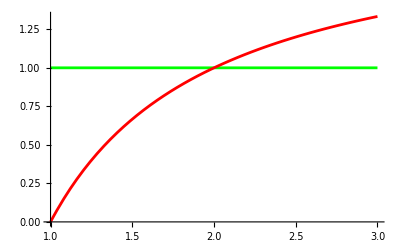

```mathematica
PlotRuleList[tr[[1]]]
```

```mathematica
EcoStableQ[tr[[1]]]
EcoStableQ[tr[[2]]]
```

Piecewise[{{True, 2 n (-1+n (-2+nk)+nk)<2 n^3+nk p&&2 n+n^2 nk+nk p>2 n^3+nk}, {False, 2 n+n^2 nk+nk p<2 n^3+nk||2 n (-1+n (-2+nk)+nk)>2 n^3+nk p}, {Indeterminate, True}}]

Piecewise[{{True, 2 n (-1+n (-2+nk)+nk)<2 n^3+nk p&&2 n+n^2 nk+nk p>2 n^3+nk}, {False, 2 n+n^2 nk+nk p<2 n^3+nk||2 n (-1+n (-2+nk)+nk)>2 n^3+nk p}, {Indeterminate, True}}]

```mathematica
EcoStableQ[tr]
```

{True,False}

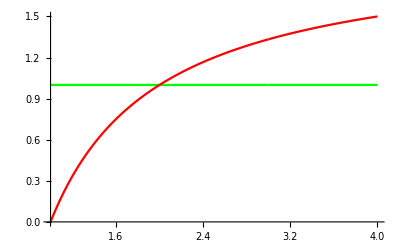

```mathematica
PlotRuleList[tr,{n,p}]
```

```mathematica
ev=Interpolation[Table[{par,EcoEigenvalues[{nk->par},Slice[tr[[1]],par]]},{par,1,3,0.01}]]
```

InterpolatingFunction[…]

```mathematica
EcoEigenvalues[tr,nk]
```

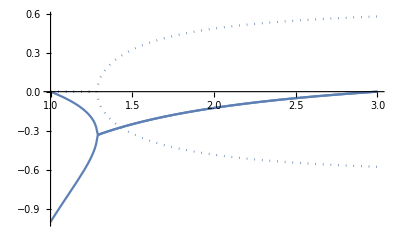

```mathematica
ReImPlot[ev[nk],{nk,1,3}]
```

```mathematica
PlotEigenvalues[]
```

```mathematica
Show[
PlotRuleList[tr[[1]],{n,p}],
PlotRuleList[tr[[2]],{n,p},LineStyles->Dashing[0.01]],
PlotRange->All
]
```

-Graphics-

```mathematica
Table[{par,EcoEigenvalues[{nk->par},Slice[tr[[1]],par]]},{par,1,2,0.1}]
```

{{1.,{-1.,-7.13501×10^-6}},{1.1,{-0.807334,-0.056302}},{1.2,{-0.614357,-0.135643}},{1.3,{-0.326924+0.0922343 ⅈ,-0.326924-0.0922343 ⅈ}},{1.4,{-0.285714+0.247436 ⅈ,-0.285714-0.247436 ⅈ}},{1.5,{-0.249996+0.322739 ⅈ,-0.249996-0.322739 ⅈ}},{1.6,{-0.218753+0.373702 ⅈ,-0.218753-0.373702 ⅈ}},{1.7,{-0.191173+0.411495 ⅈ,-0.191173-0.411495 ⅈ}},{1.8,{-0.166667+0.44096 ⅈ,-0.166667-0.44096 ⅈ}},{1.9,{-0.144737+0.464644 ⅈ,-0.144737-0.464644 ⅈ}},{2.,{-0.125+0.484123 ⅈ,-0.125-0.484123 ⅈ}}}

```mathematica
FinalSlice[tr[[1]]]
InitialSlice[tr[[2]]]
```

{n→1.,p→1.33334}

{n→1.,p→1.33334}

```mathematica
Slice[tr[[2]],3.2]
```

{n→1.,p→1.375}

## w/ eigenvalues [dead-end?]

```mathematica
(* trying to track Eigenvalues in NDSolve .. maybe not worth the trouble *)
```

#### Definition

```mathematica
TrackEq[eqnsin_List,initpar_?RuleListQ,initvars_?RuleListQ,{par_Symbol,parmin_?NumericQ,parmax_?NumericQ},opts___?OptionQ]:=Module[{
(* options *)
method,findrootopts,ndsolveopts,smin,smax,
(* other variables *)
parname,ipar,eqns,j,whenevents,unks,subrule,breaks,isol,ics,deqns,sol,s1,s2,res,respart,pts},

(* handle options *)
method=Evaluate[Method/.Flatten[{opts,Options[TrackEq]}]];
findrootopts=Evaluate[FindRootOpts/.Flatten[{opts,Options[TrackEq]}]];
ndsolveopts=Evaluate[NDSolveOpts/.Flatten[{opts,Options[TrackEq]}]];
smin=Evaluate[SMin/.Flatten[{opts,Options[TrackEq]}]];
smax=Evaluate[SMax/.Flatten[{opts,Options[TrackEq]}]];

parname=ToString[par];
ipar=par/.initpar;
eqns=eqnsin/.RHS;
unks=eqnsin[[All,1]]/.Derivative[1][var_]->var;
(*Print["unks=",unks];*)

(* jacobian *)
j:=D[eqns,{unks}]/.subrule;

(* use FindRoot to improve initial guess *)
isol=FindRoot[eqns/.initpar,initvars/.{(var_->val_)->{var,val}},Evaluate[Sequence@@findrootopts]];
If[Global`debug,Print["isol=",isol]];

whenevents={};

Which[
	method=="Direct",
	subrule=Table[unk->unk[par],{unk,unks}];
	ics=Table[unk[ipar]==(unk/.isol),{unk,unks}];
	deqns=Map[#==0&,D[eqns/.subrule,par]];
	maxev[param_?NumericQ]:=Module[{jac},jac=D[eqns,{unks}]/.subrule;Print[jac];Max[Re[Eigenvalues[jac]]]];
	whenevents=Join[whenevents,{
		WhenEvent[Evaluate[Max[Re[Eigenvalues[j]]]==0],"StopIntegration"](*,
		WhenEvent[maxev[par]==0,"StopIntegration"]*)
	}];
	Print["whenevents="];Print[whenevents];
	(* track root with NDSolve *)
	sol=NDSolve[Join[deqns,ics,whenevents],unks,{par,parmin,parmax},Evaluate[Sequence@@ndsolveopts]]⟦1⟧;
	Return[sol]
,
	method=="PseudoArcLength",
	subrule=Append[Table[unk->unk[s],{unk,unks}],par->par[s]];
	(*ev[param_?NumericQ,state_]:=ReIm/@Sort[Eigenvalues[j/.par[s]->param/.Thread[(unks/.subrule)->state]]];*)
	ev[param_?NumericQ,state_,evs_]:=ReIm/@FindEigenvalues[j/.par[s]->param/.Thread[(unks/.subrule)->state],evs.{1,I}];
(*Print[ipar];
Print[unks/.isol];
Print[ReIm/@Eigenvalues[D[eqns,{unks}]/.initpar/.initvars]];
Print["@@ ",ev[ipar,(unks/.isol),ReIm/@Eigenvalues[D[eqns,{unks}]/.initpar/.initvars]]];*)
	ics=Join[
		Table[unk[0]==(unk/.isol),{unk,unks}],
		{par[0]==ipar,λ[0]==ReIm/@Eigenvalues[D[eqns,{unks}]/.initpar/.initvars]}
	];
(*Print["ics="];Print[ics];*)
	If[Global`debug,Print["ics="];Print[ics]];
	whenevents=Join[whenevents,{
		WhenEvent[par[s]==parmax,"StopIntegration"],
		WhenEvent[par[s]==parmin,"StopIntegration"],
		WhenEvent[par'[s]==0,AppendTo[breaks,s]],
		WhenEvent[Max[λ[s][[All,1]]]==0,AppendTo[breaks,s]]
	}];
	(*Print["whenevents="];Print[whenevents];*)
	Global`deqns=deqns=Join[
		Map[#==0&,eqns/.subrule],
		{Total[D[unks/.subrule,s]]^2+D[par[s],s]^2==1},
		{par'[0]==1},
		{λ[s]==ev[par[s],unks/.subrule,λ[s]]}
	];
	If[Global`debug,Print["deqns="];Print[deqns]];
	(* track root with NDSolve *)
	breaks={}; (* capture bifurcation points *)
	Quiet[
		sol=NDSolve[Join[deqns,ics,whenevents],Join[unks,{par,λ}],{s,smin,smax},Evaluate[Sequence@@ndsolveopts]]⟦1⟧,
	{Part::partd}];
	(* beginning and ending s *)
	{s1,s2}=(par/.sol)["Domain"]⟦1⟧;
	(* add endpoints to breaks *)
	breaks=Sort[Join[{s1,s2},breaks]];
	(*Print["breaks=",breaks];*)
	(* construct interpolatingfunctions (unk vs par) for each segment (between breaks) *)
	res={};
	Do[
		respart={};
		Do[
			pts=DeleteDuplicatesBy[Chop@Join[
				{{breaks[[i]],par[breaks[[i]]],unk[breaks[[i]]]}/.sol},
				Transpose[{(par/.sol)["Coordinates"]⟦1⟧,(par/.sol)["ValuesOnGrid"],(unk/.sol)["ValuesOnGrid"]}],
				{{breaks[[i+1]],par[breaks[[i+1]]],unk[breaks[[i+1]]]}/.sol}
			],First];
			AppendTo[respart,unk->Interpolation[Select[pts,breaks⟦i⟧<=#⟦1⟧≤breaks⟦i+1⟧&]⟦All,2;;3⟧,"ExtrapolationHandler"->{Indeterminate&,"WarningMessage"->False}]];
		,{unk,unks}];
		pts=DeleteDuplicatesBy[Chop@Join[
			{{breaks[[i]],par[breaks[[i]]],λ[breaks[[i]]]}/.sol},
			Transpose[{(par/.sol)["Coordinates"]⟦1⟧,(par/.sol)["ValuesOnGrid"],(λ/.sol)["ValuesOnGrid"]}],
			{{breaks[[i+1]],par[breaks[[i+1]]],λ[breaks[[i+1]]]}/.sol}
		],First];
		pts=Map[{#[[1]],#[[2]],#[[3]].{1,I}}&,pts];
		AppendTo[respart,Eigenvalues->Interpolation[Select[pts,breaks⟦i⟧<=#⟦1⟧≤breaks⟦i+1⟧&]⟦All,2;;3⟧,"ExtrapolationHandler"->{Indeterminate&,"WarningMessage"->False}]];
		AppendTo[res,respart];
	,{i,Length[breaks]-1}];
	Return[res]
	,
	Else,
	Message[TrackRoot::badmtd];Return[$Failed]
];

]
```

```mathematica
PacletDirectoryAdd["~/github/EcoEvo"];
<<EcoEvo`
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

EcoEvo Package Version 1.8.0 (June 16, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Pop[n]->{Equation:>n(1-n/nk)-an p n/(n+h),Color->Green},
Pop[p]->{Equation:>p(apred n/(n+h)-mp),Color->Red},
Parameters:>{an>0,apred>0,h>0,mp>0,nk>0}
}];
```

```mathematica
RuleListSet@{an->1,apred->2,h->1,mp->1,nk->2}
Clear[nk]
```

```mathematica
EcoEqns[]
```

{n'==n (1-n/nk)-(n p)/(1+n),p'==(-1+(2 n)/(1+n)) p}

```mathematica
debug=False;
tr=TrackEq[EcoEqns[],{nk->1.1},{n->1,p->0.181818},{nk,1,4}]
```

ics=

{n[0]==1.,p[0]==0.181818,nk[0]==1.1,EcoEvo`Private`λ[0]=={{-0.807334,0},{-0.056302,0}}}

{{n→InterpolatingFunction[…],p→InterpolatingFunction[…],Eigenvalues→InterpolatingFunction[…]},{n→InterpolatingFunction[…],p→InterpolatingFunction[…],Eigenvalues→InterpolatingFunction[…]}}

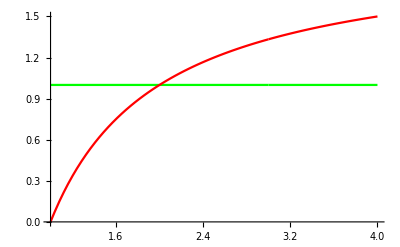

```mathematica
PlotRuleList[tr,{n,p}]
```

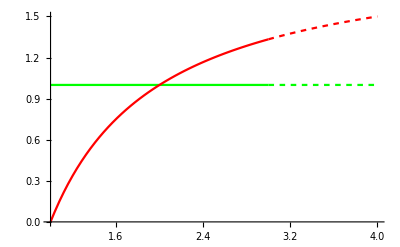

```mathematica
Show[
PlotRuleList[tr[[1]],{n,p}],
PlotRuleList[tr[[2]],{n,p},LineStyles->Dashing[0.01]],
PlotRange->All
]
```

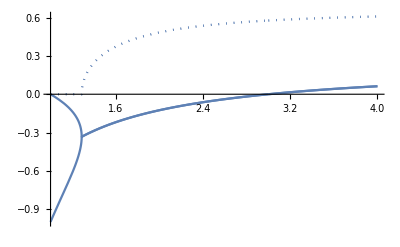

```mathematica
PlotRuleList[tr,Eigenvalues]
```

```mathematica
FinalSlice[tr[[1]]]
InitialSlice[tr[[2]]]
```

{n→1.,p→1.33333,Eigenvalues→{8.81913×10^-9+0.577351 ⅈ,8.81913×10^-9+0.577351 ⅈ}}

{n→1.,p→1.33333,Eigenvalues→{8.81913×10^-9+0.577351 ⅈ,8.81913×10^-9+0.577351 ⅈ}}

```mathematica
Slice[tr[[2]],3.2]
```

{n→1.,p→1.37497,Eigenvalues→{0.015615+0.586082 ⅈ,0.015615+0.586082 ⅈ}}

```mathematica
nk=2;
SolveEcoEq[][[-1]]
```

{n→1,p→1}

```mathematica
Clear[nk]
tr=TrackEq[EcoEqns[],{nk->2.},{n->1,p->1},{nk,1,4}]
```

ics=

{n[0]==1.,p[0]==1.,nk[0]==2.,EcoEvo`Private`λ[0]=={{-0.125,0.484123},{-0.125,-0.484123}}}

NDSolve::index: The DAE solver failed at EcoEvo`Private`s = -0.91176. The solver is intended for index 1 DAE systems and structural analysis indicates that the DAE index is 2. The option Method->{"IndexReduction"->Automatic} may be used to reduce the index of the system.

{{n→InterpolatingFunction[…],p→InterpolatingFunction[…],Eigenvalues→InterpolatingFunction[…]},{n→InterpolatingFunction[…],p→InterpolatingFunction[…],Eigenvalues→InterpolatingFunction[…]}}

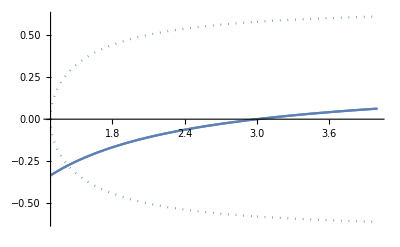

```mathematica
PlotRuleList[tr,Eigenvalues]
```